### 2. Теоремы о вычетах и их применение к вычислению конурных интегралов.

П е р в а я  т е о р е м а  о  в ы ч е т а х. Если функция f(z) аналитична в области D, за исключением изолированных особых точек z_1,... z_k, лежащих в этой области, то для любого простого замкнутого контура C⊂D, охватывающего точки z_1,... z_k:

∫_(С^+) f(z)ⅆz=2πⅈ∑_(k=1)^N res(f(z);z_k)

В т о р а я  т е о р е м а  о  в ы ч е т а х.

№12.434 Используя теоремы о вычетах, вычислить следующий интеграл:

∫_(C^+) z/((z-1)(z-2))ⅆz,  C={z | |z-2|=2}

Для этого воспользуемся Первой теоремой о вычетах:

Найдем все полюса функции f(z)

```mathematica
f[z_]:=z/((z-1)(z-2))
```

Конечно видно, что полюсами будут точки z_1=1 и z_2=2, но всё же применим более общий способ:

```mathematica
sol=Solve[f[z]^-1==0,z]
```

{{z→1},{z→2}}

Теперь нужно определить, какие из найденных полюсов охватываются контуром С.

1) Определим графически.

Для этого изобразим контур С, и найденые нами полюса.

```mathematica
Show[ ContourPlot[(x-2)^2+y^2==4,{x,0,4},{y,-2,2},AxesLabel->{Re,Im},PlotRange->{{-1,5},{-3,3}} ,Frame->False,Axes->True],Graphics[{PointSize[Large],Red,Point[ReIm[z/.sol]]} ] ]
```

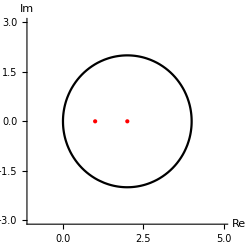

Из рисунка видно, что обе точки лежат внутри контура С.

Найдем интеграл по первой теореме вычетов (1).

```mathematica
int=2π ⅈ Sum[Residue[f[z],{z,z/.sol[[i]]}],{i,1,Length[sol]}]
```

2 ⅈ π

2) Определим аналитически.

Будем брать каждый i-ый полюс,проверять растояние от него до точки (2,0) - центра окружности, и если оно меньше заданного радиуса, будем считать в нем вычет.

```mathematica
int1=2π ⅈ Sum [ If[ Abs[ -2+z/.sol[[i]]]≤ 2,Residue[f[z],{z,z/.sol[[i]] } ],0],{i,1,Length[z/.sol]} ]
```

2 ⅈ π

Итак конечный ответ:

∫_(C^+) z/((z-1)(z-2))ⅆz=2 ⅈ π

Это общий алгоритм решения такого класса задач, в которых НЕТ существенно особых точек, используя который можно, заменяя вверху функцию f(z) на одну из тех, которые есть в задачах №№ 12.435-449 получить ответы их решения (см. таблицу ответов). Читатель же теперь может найти эти решения и ответы самостоятельно.

Мне кажется вот такие супералгоритмы для решения всего блока задач выглядят совсем не к месту, мне кажется стоит найти другой способ как подать ответы на задачи для самостоятельного решения

```mathematica
F[z_]:={{E^z/(z^2(z^2+9)),0,1},{Sin[z]/(z^2+9),0,4},{1/((z-1)^2(z^2+1)),0,1},{(z+1)/(E^z+1),0,4},{(1-E^(z^2))/(z^2(z-I)),I,2},{E^z/(z^4+2 z^2+1),I,1},{z^3/(2 z^4+1),0,1}}
```

```mathematica
Grid[Table[ {"∮",F[z][[i,1]],"ⅆ z =",2π ⅈ Sum[Boole[Abs[-F[z][[i,2]]+z/.DeleteDuplicates[Solve[(F[z][[i,1]])^-1==0,z]][[k]]]≤ F[z][[i,3]]]Residue[F[z][[i,1]],{z,z/.DeleteDuplicates[Solve[(F[z][[i,1]])^-1==0,z]][[k]]}],{k,1,Length@DeleteDuplicates[Solve[(F[z][[i,1]])^-1==0,z]]}]},{i,1,Length[F[z]]}]]
```

∮ | ⅇ^z/(z^2 (9+z^2)) | ⅆ z = | (2 ⅈ π)/9
∮ | Sin[z]/(9+z^2) | ⅆ z = | 2/3 ⅈ π Sinh[3]
∮ | 1/((-1+z)^2 (1+z^2)) | ⅆ z = | 0
∮ | (1+z)/(1+ⅇ^z) | ⅆ z = | 2 π (-ⅈ+π)
∮ | (1-ⅇ^(z^2))/(z^2 (-ⅈ+z)) | ⅆ z = | (2 ⅈ (1-ⅇ) π)/ⅇ
∮ | ⅇ^z/(1+2 z^2+z^4) | ⅆ z = | (1/2-ⅈ/2) ⅇ^ⅈ π
∮ | z^3/(1+2 z^4) | ⅆ z = | ⅈ π